```mathematica
FormatAdjacencyMatrix[g_,highligh_:{}]:=Block[{vertices=Sort[VertexList[g]],mat, value},
mat=Table[
Table[
value=If[i==j,"◆",If[EdgeQ[g,i<->j],Style["●",Darker[Green]],Style["●",Darker[Red]]]];
If[MemberQ[highligh,i]||MemberQ[highligh,j],Framed[value,FrameMargins->None,FrameStyle->Gray],value]
,{j,vertices}
]
,{i,vertices}
];
MatrixForm[mat,
TableHeadings->{vertices,Map[Rotate[#,-Pi/2]&,vertices]}]
]
```

```mathematica
FormatAdjacencyMatrix[Graph[plantri[[1]]],{1,3,5}]
```

( | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆)

```mathematica
FormatAdjacencyMatrix2[g_,highligh_:{},sym_:{}]:=Block[{vertices=Sort[VertexList[g]],mat, value,sets,sets2,mat2,labels,colors,vertexpos=Association[]},
If[sym=={},sym=First[FindFullFormula4[g]]];
mat=Table[
Table[
value=If[i==j,"◆",If[EdgeQ[g,i<->j],Style["●",Darker[Green]],Style["●",Darker[Red]]]];
If[MemberQ[highligh,i]||MemberQ[highligh,j],Framed[value,FrameMargins->None,FrameStyle->Gray],value]
,{j,vertices}
]
,{i,vertices}
];
sets=SymbolToSets[sym];
Table[vertexpos[vertices[[i]]]=i,{i,Length[VertexList[g]]}];
sets2=Flatten[sets];
colors=Association[SymbolToColoring[sym]];
labels=Map[Style[#,colors[#]]&,sets2];
mat2=Table[Table[mat[[vertexpos[sets2[[i]]],vertexpos[sets2[[j]]]]],{i,Length[mat]}],{j,Length[mat]}];
MatrixForm[mat2,
TableHeadings->{labels,Map[Rotate[#,-Pi/2]&,labels]}]
]
```

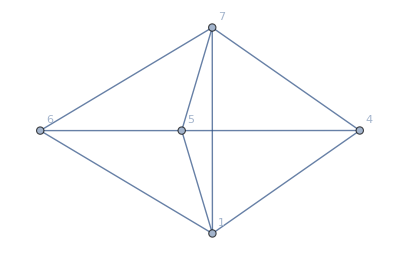

```mathematica
Graph[{5<->4,6<->5,7<->4,7<->5,7<->6,1<->4,1<->5,1<->6,1<->7},VertexLabels->"Name"]
```

```mathematica
FormatAdjacencyMatrix2[Graph[{5<->4,6<->5,7<->4,7<->5,7<->6,1<->4,1<->5,1<->6,1<->7}],{5,1,6,7}]
```

( | 1 | 4 | 6 | 5 | 7
1 | ◆ | ● | ● | ● | ●
4 | ● | ◆ | ● | ● | ●
6 | ● | ● | ◆ | ● | ●
5 | ● | ● | ● | ◆ | ●
7 | ● | ● | ● | ● | ◆)

```mathematica
FormatAdjacencyMatrix2[Graph[plantri[[1]]],{1,3,5}]
```

( | 1 | 9 | 11 | 2 | 5 | 12 | 3 | 7 | 10 | 4 | 6 | 8
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
9 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
11 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
12 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆)